```mathematica
(***  Mathematica notebook with the modules for the DGIG distribution  (PDF, CDF and Quantiles), modules DGIGpdf, DGIGcdf and DGIGquant ***)
```

```mathematica
Rat[x_]:=Module[{nn},
If [ToString[Head[x]]≠"Real",x,
nn=StringLength[ToString[x,InputForm]]-1;Round[x*10^nn]/10^nn]]

SetAttributes[Rat,Listable]

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Table[c=ReplacePart[c,(Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}])/(r[[i]]-1)!,{i,r[[i]]}],{i,1,p}];
Table[Table[c=ReplacePart[c,Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{i,r[[i]]-k}],{k,1,r[[i]]-1}],{i,1,p}];
c
]

P[c_,d_,r1_,r2_,l1_,l2_,z_]:=Table[Sum[c[[j]][[k]]*Sum[Sum[d[[ell]][[h]]*Sum[Binomial[k-1,i]*z^(k-1-i)*(h+i-1)!/(l1[[j]]+l2[[ell]])^(h+i),{i,0,k-1}],{h,1,r2[[ell]]}],{ell,1,Length[r2]}],{k,1,r1[[j]]}],{j,1,Length[r1]}];

(* Computation for z=0 *)

P0[c_,d_,r1_,r2_,l1_,l2_,z_]:=Table[Sum[c[[j]][[k]]*Sum[Sum[d[[ell]][[h]]*(h+k-2)!/(l1[[j]]+l2[[ell]])^(h+k-1),{h,1,r2[[ell]]}],{ell,1,Length[r2]}],{k,1,r1[[j]]}],{j,1,Length[r1]}];

DGIGpdf[r1_,r2_,li1_,li2_,zi_,prec_:30]:=Module[{p1,p2,p3,l1,l2,z,c,d,PP,K1,K2},If[Count[r1,_Integer]==Length[r1]&&Count[r2,_Integer]==Length[r2]&&And@@Positive[r1]&& And@@Positive[r2]&&And@@Positive[li1]&&And@@Positive[li2]&&Length[r1]==Length[li1]&&Length[r2]==Length[li2],
p1=Length[r1];
p2=Length[r2];
l1=Rat[li1];
l2=Rat[li2];
z=Rat[zi];
c=Makec[r1,l1,p1];
d=Makec[r2,l2,p2];
PP=If[z>0,P[c,d,r1,r2,l1,l2,z],If[z==0,P0[c,d,r1,r2,l1,l2,z],P[d,c,r2,r1,l2,l1,-z]]];
K1=Product[l1[[j]]^r1[[j]],{j,1,p1}];
K2=Product[l2[[j]]^r2[[j]],{j,1,p2}];
SetPrecision[If[z>0,K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],If[z==0,K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],K1*K2*Sum[PP[[ell]]*Exp[l2[[ell]]*z],{ell,1,p2}]]],prec]
]
]

DGIGpdf::usage="DGIGpdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG pdf.
It has 6 arguments (the first 5 are mandatory):
r1 - list of the shape parameters for the Gamma distributions with positive sign;
r2 - list of the shape parameters for the Gamma distributions with negative sign;
l1 - list of the rate parameters for the Gamma distributions with positive sign;
l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the PDF has to be computed;
prec - number of precision digits to be used in the display of results (default value 30)";

DGIGpdfsimp[r1_,r2_,li1_,li2_,zi_,c_,d_,K1_,K2_,prec_:30]:=Module[{p1,p2,p3,l1,l2,z,PP},If[Count[r1,_Integer]==Length[r1]&&Count[r2,_Integer]==Length[r2]&&And@@Positive[r1]&& And@@Positive[r2]&&And@@Positive[li1]&&And@@Positive[li2]&&Length[r1]==Length[li1]&&Length[r2]==Length[li2],
p1=Length[r1];
p2=Length[r2];
l1=Rat[li1];
l2=Rat[li2];
z=Rat[zi];
PP=If[z>0,P[c,d,r1,r2,l1,l2,z],If[z==0,P0[c,d,r1,r2,l1,l2,z],P[d,c,r2,r1,l2,l1,-z]]];
SetPrecision[If[z>0,K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],If[z==0,K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],K1*K2*Sum[PP[[ell]]*Exp[l2[[ell]]*z],{ell,1,p2}]]],prec]
]
]

PS[c_,d_,r1_,r2_,l1_,l2_,z_]:=Table[Sum[c[[j]][[k]]*Sum[Sum[d[[ell]][[h]]*Sum[Binomial[k-1,i]*(h+i-1)!/(l1[[j]]+l2[[ell]])^(h+i)*Sum[(k-1-i)!/t!*If[z==0&&t==0,1,z^t]/l1[[j]]^(k-i-t),{t,0,k-1-i}],{i,0,k-1}],{h,1,r2[[ell]]}],{ell,1,Length[r2]}],{k,1,r1[[j]]}],{j,1,Length[r1]}];

DGIGcdf[r1_,r2_,li1_,li2_,zi_,prec_:30]:=Module[{p1,p2,l1,l2,c,d,PP,K1,K2,z},
If[Count[r1,_Integer]==Length[r1]&&Count[r2,_Integer]==Length[r2]&&And@@Positive[r1]&& And@@Positive[r2]&&And@@Positive[li1]&&And@@Positive[li2]&&Length[r1]==Length[li1]&&Length[r2]==Length[li2],
p1=Length[r1];
p2=Length[r2];
l1=Rat[li1];
l2=Rat[li2];
z=Rat[zi];
c=Makec[r1,l1,p1];
d=Makec[r2,l2,p2];
PP=If[z≥0,PS[c,d,r1,r2,l1,l2,z],PS[d,c,r2,r1,l2,l1,-z]];
K1=Product[l1[[j]]^r1[[j]],{j,1,p1}];
K2=Product[l2[[j]]^r2[[j]],{j,1,p2}];
SetPrecision[If[z≥0,1-K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],K1*K2*Sum[PP[[ell]]*Exp[l2[[ell]]*z],{ell,1,p2}]],prec]
]
]

DGIGcdf::usage="DGIGcdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG cdf.
It has 6 arguments (the first 5 are mandatory):
r1 - list of the shape parameters for the Gamma distributions with positive sign;
r2 - list of the shape parameters for the Gamma distributions with negative sign;
l1 - list of the rate parameters for the Gamma distributions with positive sign;
l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the PDF has to be computed;
prec - number of precision digits to be used in the display of results (default value 30)";

DGIGcdfsimp[r1_,r2_,li1_,li2_,zi_,c_,d_,K1_,K2_,prec_:30]:=Module[{p1,p2,l1,l2,PP,z},
If[Count[r1,_Integer]==Length[r1]&&Count[r2,_Integer]==Length[r2]&&And@@Positive[r1]&& And@@Positive[r2]&&And@@Positive[li1]&&And@@Positive[li2]&&Length[r1]==Length[li1]&&Length[r2]==Length[li2],
p1=Length[r1];
p2=Length[r2];
l1=Rat[li1];
l2=Rat[li2];
z=Rat[zi];
PP=If[z≥0,PS[c,d,r1,r2,l1,l2,z],PS[d,c,r2,r1,l2,l1,-z]];
SetPrecision[If[z≥0,1-K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],K1*K2*Sum[PP[[ell]]*Exp[l2[[ell]]*z],{ell,1,p2}]],prec]
]
]


DGIGquant[r1_,r2_,l1_,l2_,qquant_,xoo_:1,eps_:10^-11,pp_:11,preco_:50]:=Module[{quant,xo,prec,vec,p,ll,c,pr,xa,xb,res,nx,F,F1,F2},
quant=Rat[qquant];
If[TrueQ[xoo==1||xoo==Null],xo=1,xo=Rat[xoo]];
prec=preco;
F[x_,pr_]:=DGIGcdf[r1,r2,l1,l2,x,pr];
While[Length[RealDigits[res=F[xo,prec]][[1]]]<25*pp,prec=3*prec];
If[res>quant,xa=xo;xo=xo-1;While[F[xo,prec]>quant,xa=xo;xo=xo-1],
xa=xo;xo=xo+1;While[F[xo,prec]<quant,xa=xo;xo=xo+1]];
If[xo>xa,xb=xo,xb=xa;xa=xo];
xo=(xa+xb)/2;
res=F[xo,prec];
While[Abs[res-quant]>Min[10^-3,quant/10],xo=(xa+xb)/2;
If[(res=F[xo,prec])>quant,xb=xo,xa=xo]];
nx=Rat[xo];
xa=0;
F1[x_,pr_]:=DGIGpdf[r1,r2,l1,l2,x,pr];
F2[x_,pr_]:=DGIGcdf[r1,r2,l1,l2,x,pr];
While[Abs[nx-xa]>eps,{xa=nx;nx=xa+(quant-F2[Rat[xa],prec])/F1[Rat[xa],prec]}];SetPrecision[nx,Max[pp,-Log[10,eps]]]]

DGIGquant2[r1_,r2_,l1_,l2_,qquant_,xoo_:1,eps_:10^-11,pp_:11,preco_:50]:=Module[{quant,xo,prec,vec,p,ll,c,d,K1,K2,pr,xa,xb,res,nx,F,F1,F2,ll1,ll2,p1,p2},
quant=Rat[qquant];
If[TrueQ[xoo==1||xoo==Null],xo=1,xo=Rat[xoo]];
prec=preco;
p1=Length[r1];
p2=Length[r2];
ll1=Rat[l1];
ll2=Rat[l2];
c=Makec[r1,ll1,p1];
d=Makec[r2,ll2,p2];
K1=Product[ll1[[j]]^r1[[j]],{j,1,p1}];
K2=Product[ll2[[j]]^r2[[j]],{j,1,p2}];
F[x_,pr_]:=DGIGcdfsimp[r1,r2,l1,l2,x,c,d,K1,K2,pr];
While[Length[RealDigits[res=F[xo,prec]][[1]]]<preco,prec=2*prec];
If[res>quant,xa=xo;If[xo>0,xo=xo/1.5,xo=xo*1.5];While[F[xo,prec]>quant,xa=xo;If[xo>0,xo=xo/1.5,xo=xo*1.5]],
xa=xo;If[xo>0,xo=xo*1.5,xo=xo/1.5];While[F[xo,prec]<quant,xa=xo;If[xo>0,xo=xo*1.5,xo=xo/1.5]]];
If[xo>xa,xb=xo,xb=xa;xa=xo];
xo=(xa+xb)/2;
res=F[xo,prec];
While[Abs[res-quant]>Min[10^-3,quant/10],xo=(xa+xb)/2;If[(res=F[xo,prec])>quant,xb=xo,xa=xo]];
nx=Rat[xo];
xa=0;
F1[x_,pr_]:=DGIGpdfsimp[r1,r2,l1,l2,x,c,d,K1,K2,pr];
F2[x_,pr_]:=DGIGcdfsimp[r1,r2,l1,l2,x,c,d,K1,K2,pr];
While[Abs[nx-xa]>eps,{xa=nx;nx=xa+(quant-F2[Rat[xa],prec])/F1[Rat[xa],prec]}];SetPrecision[nx,Max[preco,-Log[10,eps]]]]

DGIGquant::usage="DGIGquant[r1  ,r2  ,ll1  ,ll2  ,q  ,xo  ,eps  ,pp  ,prec]
Gives the value for the quantile 'q' of a DGIG distribution with sets of integer shape parameters 'r1' and 'r2', and sets of rate parameters 'll1' and 'll2';
Mandatory arguments:
'r1'  - first list of integer shape parameters;
'r2'  - second list of integer shape parameters;
'll1' - first list of rate parameters;
'll2' - second list of rate parameters;
'q' - required quantile (value between 0 and 1);
Optional arguments are:
'xo' - initial value for the search of the quantile (default value: 1)
           ==> although very commonly it is not necessary, may be useful to provide a good initial value, for example based in a plot of the cdf;
'eps' - value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11);
'pp' - number of digits for printing the quantile value (default value: maximum between 11 and -Log10 of 'eps');
'prec' - number of digits used for the intermediate computations in the module (default value: 150)]";
```

```mathematica
?DGIGpdf
```

DGIGpdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG pdf.
It has 6 arguments (the first 5 are mandatory):
r1 - list of the shape parameters for the Gamma distributions with positive sign;
r2 - list of the shape parameters for the Gamma distributions with negative sign;
l1 - list of the rate parameters for the Gamma distributions with positive sign;
l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the PDF has to be computed;
prec - number of precision digits to be used in the display of results (default value 30)

```mathematica
?DGIGcdf
```

DGIGcdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG cdf.
It has 6 arguments (the first 5 are mandatory):
r1 - list of the shape parameters for the Gamma distributions with positive sign;
r2 - list of the shape parameters for the Gamma distributions with negative sign;
l1 - list of the rate parameters for the Gamma distributions with positive sign;
l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the PDF has to be computed;
prec - number of precision digits to be used in the display of results (default value 30)

0.36413228478591120094172994529

0.84168161531047339089490002379

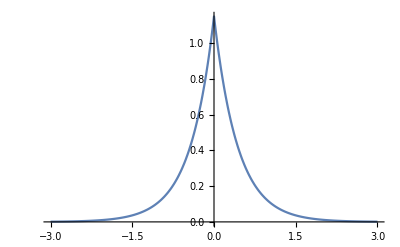

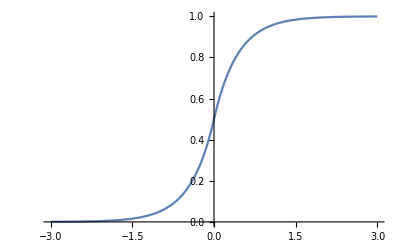

```mathematica
r1={1};
m1={23/10};
r2=r1;
m2=m1;
z=.5;
DGIGpdf[r1,r2,m1,m2,z]
DGIGcdf[r1,r2,m1,m2,z]
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-3,3}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-3,3}]
```

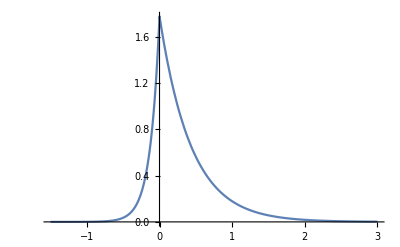

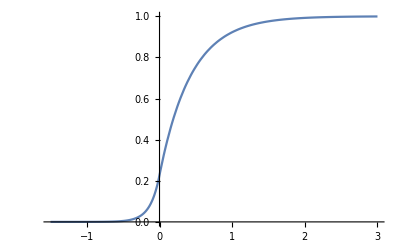

```mathematica
r1={1};
m1={23/10};
r2=r1;
m2={78/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-1.5,3},PlotRange->All]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-1.5,3}]
```

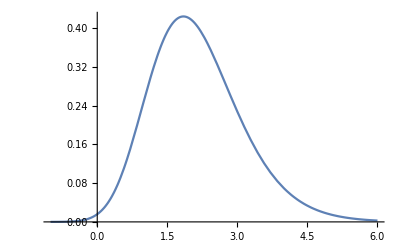

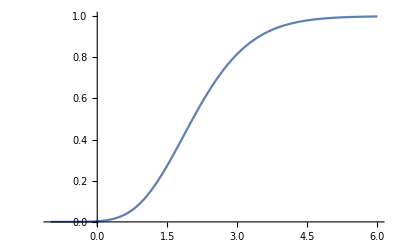

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};r2={6,7};m2={123/10,154/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-1,6}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-1,6}]
```

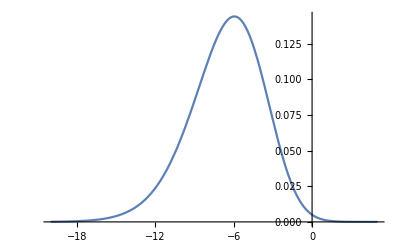

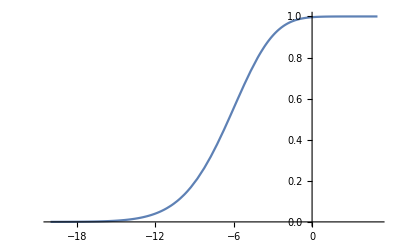

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};r2={6,7};m2={12/10,15/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-20,5}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-20,5}]
```

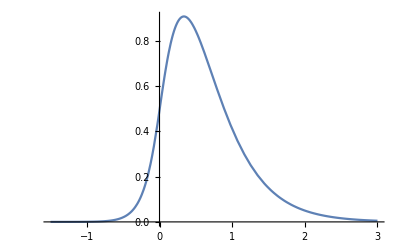

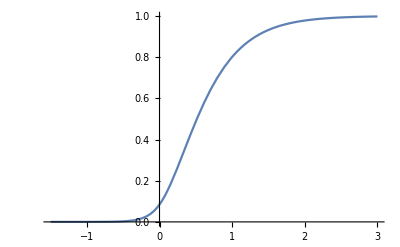

```mathematica
r1={1,1,1};m1={23/10,44/10,56/10};r2={1,1};m2={78/10,98/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-1.5,3},PlotRange->All]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-1.5,3}]
```

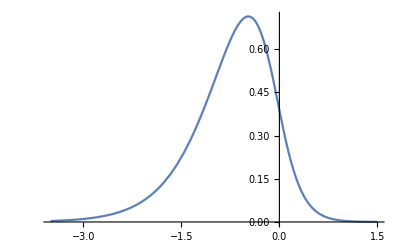

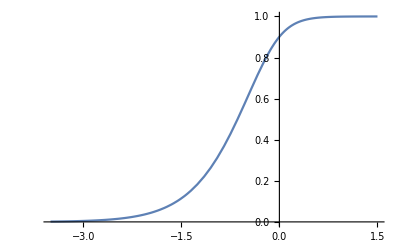

```mathematica
r1={1,1,1};m1={78/10,98/10,56/10};r2={1,1,1,1};m2={23/10,44/10,56/10,34/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-3.5,1.5},PlotRange->All]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-3.5,1.5}]
```

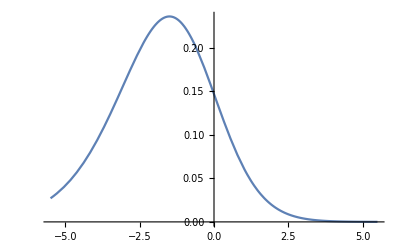

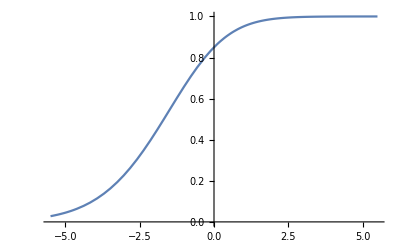

```mathematica
r1={3,4,5};
m1={23/10,45/10,56/10};
m2={67/10,15/10,37/10,54/10};
r2={2,4,5,3};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

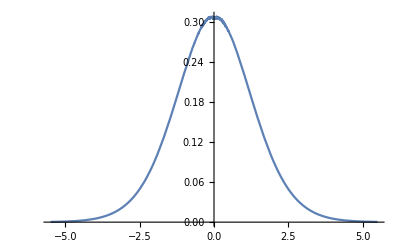

```mathematica
r1={3,4,5};
m1={23/10,45/10,56/10};
r2=r1;
m2=m1;
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5},PlotRange->All]
```

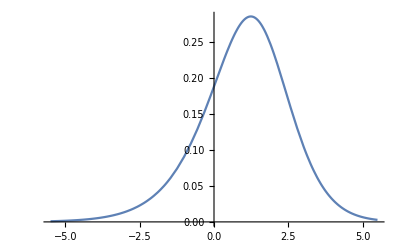

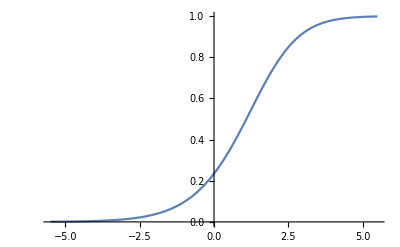

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

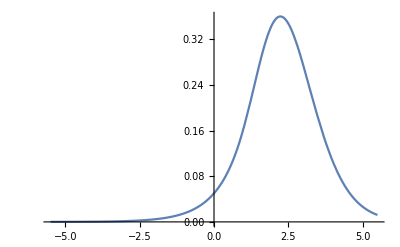

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};
r2={1};m2={12/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

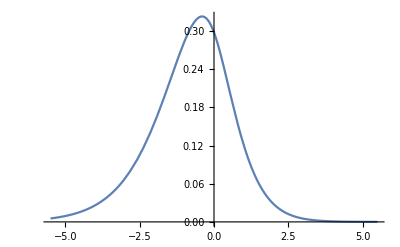

```mathematica
r1={3};m1={23/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

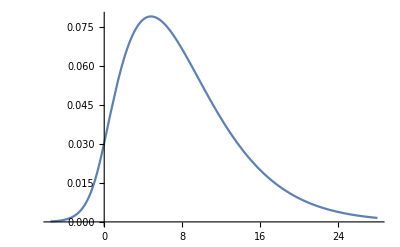

```mathematica
r1={3};m1={3/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,28}]
```

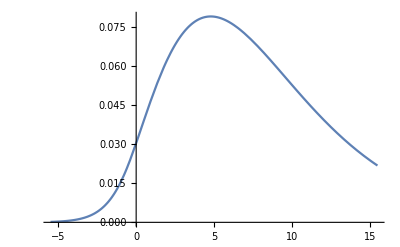

```mathematica
r1={3};m1={3/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,15.5},PlotRange->All]
```

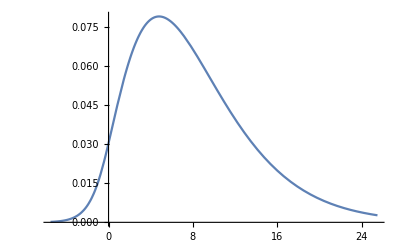

```mathematica
r1={3};m1={3/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,25.5},PlotRange->All]
```

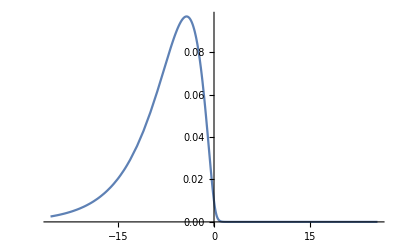

```mathematica
r1={3};m1={53/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25.5,25.5}]
```

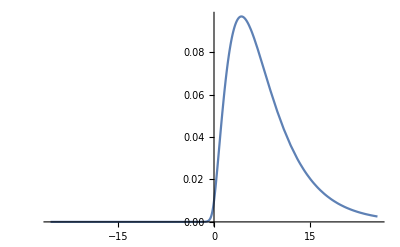

```mathematica
r1={3};m1={53/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r2,r1,m2,m1,x],{x,-25.5,25.5}]
```

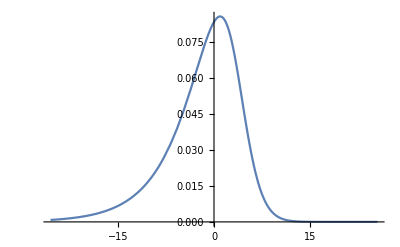

```mathematica
r1={3,5,7};m1={53/10,74/10,26/20};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25.5,25.5}]
```

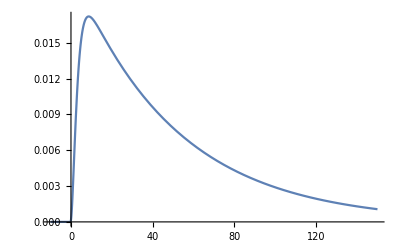

```mathematica
r1={3};m1={153/10};
r2={1,1,1};m2={2/100,5/10,7/10};
Plot[DGIGpdf[r2,r1,m2,m1,x],{x,-10,150}]
```

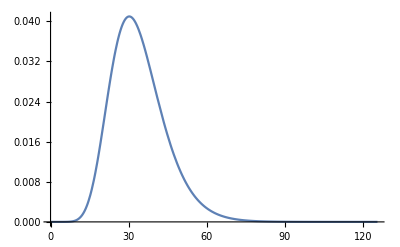

```mathematica
r1={3,5,7};m2={53/10,74/10,26/20};
r2={1,1,1};m1={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,0,125.5}]
```

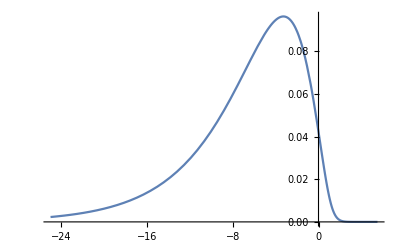

```mathematica
r1={3,5,7};m1={153/10,174/10,126/20};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25,5.5}]
```

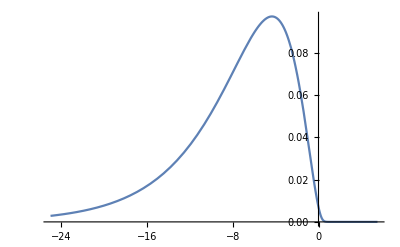

```mathematica
r1={3,5};m1={153/10,174/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25,5.5}]
```

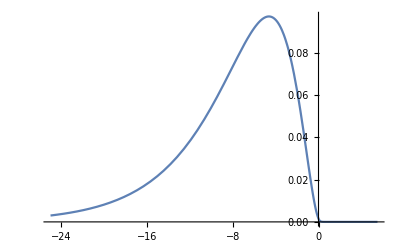

```mathematica
r1={3};m1={153/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25,5.5}]
```

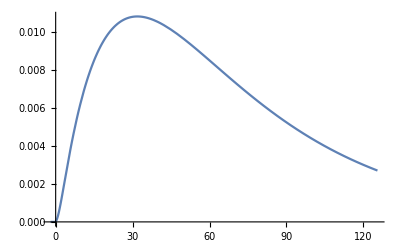

```mathematica
r2={3};m2={153/10};
r1={1,1,1};m1={2/100,5/100,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-2,125.5}]
```

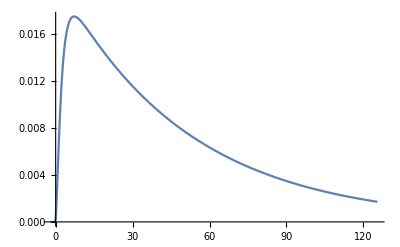

```mathematica
r2={3};m2={153/10};
r1={1,1,1};m1={2/100,5/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-2,125.5}]
```

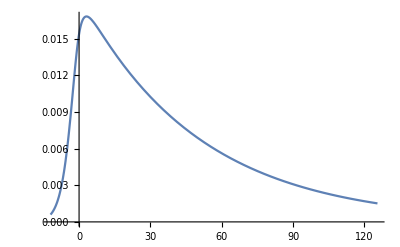

```mathematica
r2={3,3};m2={153/10,5/10};
r1={1,1,1};m1={2/100,5/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-12,125.5}]
```

```mathematica
r1={3,4,5};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
z=2.3;
Clear[x];
Quiet[NIntegrate[DGIGpdf[r1,r2,m1,m2,x],{x,-Infinity,Rat[z]},WorkingPrecision->32]]
DGIGcdf[r1,r2,m1,m2,z]
```

0.94945106294893205487100290870169

0.9494510629489320548710029087

```mathematica
?DGIGquant
```

DGIGquant[r1  ,r2  ,ll1  ,ll2  ,q  ,xo  ,eps  ,pp  ,prec]
Gives the value for the quantile 'q' of a DGIG distribution with sets of integer shape parameters 'r1' and 'r2', and sets of rate parameters 'll1' and 'll2';
Mandatory arguments:
'r1'  - first list of integer shape parameters;
'r2'  - second list of integer shape parameters;
'll1' - first list of rate parameters;
'll2' - second list of rate parameters;
'q' - required quantile (value between 0 and 1);
Optional arguments are:
'xo' - initial value for the search of the quantile (default value: 1)
           ==> although very commonly it is not necessary, may be useful to provide a good initial value, for example based in a plot of the cdf;
'eps' - value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11);
'pp' - number of digits for printing the quantile value (default value: maximum between 11 and -Log10 of 'eps');
'prec' - number of digits used for the intermediate computations in the module (default value: 150)]

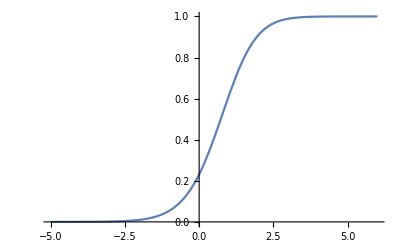

```mathematica
r1={3,4,5};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-5,6}]
```

```mathematica
r1={3,4,5};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
q1=DGIGquant[r1,r2,m1,m2,.05]
q2=DGIGquant[r1,r2,m1,m2,.95]
DGIGcdf[r1,r2,m1,m2,q1]
DGIGcdf[r1,r2,m1,m2,q2]
```

-1.0548304132

2.3054575607

0.05000000000000000000000000584

0.94999999999999999999999991131

```mathematica
r1={3,4,5};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
q1=DGIGquant[r1,r2,m1,m2,.05,-.75]
q2=DGIGquant[r1,r2,m1,m2,.95,1]
DGIGcdf[r1,r2,m1,m2,q1]
DGIGcdf[r1,r2,m1,m2,q2]
```

-1.0548304132

2.3054575607

0.050000000000000000000005361338

0.94999999999999999999999991131

```mathematica
q1=DGIGquant[r1,r2,m1,m2,.05,-2]
q2=DGIGquant[r1,r2,m1,m2,.95,3]
DGIGcdf[r1,r2,m1,m2,q1]
DGIGcdf[r1,r2,m1,m2,q2]
```

-1.0548304132

2.3054575607

0.05000000000000000000000000584

0.94999999999999999999999991131

```mathematica
r1={3,4,5};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
q1=DGIGquant[r1,r2,m1,m2,.05,,10^-20]
q2=DGIGquant[r1,r2,m1,m2,.95,,10^-20]
DGIGcdf[r1,r2,m1,m2,q1]
DGIGcdf[r1,r2,m1,m2,q2]
DGIGcdf[r1,r2,m1,m2,q1,50]
DGIGcdf[r1,r2,m1,m2,q2,50]
```

-1.0548304132175364316

2.305457560717974126

0.05

0.95

0.04999999999999999999999999999999999999988699961317

0.9499999999999999999999999999999999999998583223521

```mathematica
DGIGpdf[{1,2,3},{4,5,6},{2.1,3.4,5.6},{3.2,4.5,6.2},2.3]
```

0.0014923293649269513739182554456

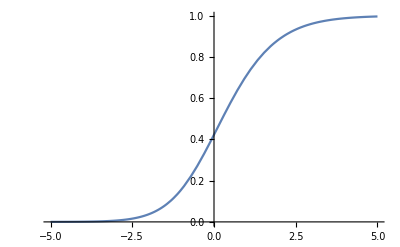

```mathematica
Plot[DGIGcdf[{1,2,3},{2,3,4},{1.2,2.3,3.4},{2.3,4.5,5.6},x],{x,-5,5}]
```

```mathematica
ClearSystemCache[];Timing[DGIGquant[{1,2,3},{2,3,4},{1.2,2.3,3.4},{2.3,4.5,5.6},0.05,-2,10^-16]]
```

1  -1.6666666666666665186

2  -1.8333333333333332593

3  -1.75

4  -1.7916666666666665186

5  -1.8125

{0.0625,-1.808736329502915}

```mathematica
ClearSystemCache[];Timing[DGIGquant[{1,2,3},{2,3,4},{1.2,2.3,3.4},{2.3,4.5,5.6},0.05,-1.8,10^-16]]
```

1  -2.25

2  -2.0249999999999999112

3  -1.9125000000000000888

4  -1.8562500000000001776

5  -1.828125

6  -1.8140624999999999112

{0.0625,-1.808736329502915}

```mathematica
DGIGcdf[{1,2,3},{2,3,4},{1.2,2.3,3.4},{2.3,4.5,5.6},-1.80873632950291548224391437033163073156`16.]
```

0.05

```mathematica
SetPrecision[c,30]
```

{{0.0138009557161833456966894957476,1.,1.},{0.0429409346938099177595218744152,-0.0722418077789978616424897416633,1.},{-0.0567418904099932634562113701628,-0.0705315935540256673668716171668,-0.0295159386068476977567886658796}}

```mathematica
SetPrecision[d,30]
```

{{-0.0165257686154896099642802494467,0.00698311571991583612071711602867,-0.00107993086683870073368493853224,0.0000615750055653645155171236882419,1.,1.},{0.0454892848287761744288640248499,-0.0119066603016854561510786341607,0.0168544420811132697158905711044,-0.00109393001466256464235295630369,0.00060439633310106696490000835779,1.},{-0.0289635162132865644645837754032,-0.0228309337806810466058665757727,-0.00784859366903512909797069598294,-0.00148148448955801391628208826988,-0.000154862209053271894708765112679,-7.24584647863932718362111995101×10^-6}}

```mathematica
SetPrecision[PP,20]
```

{4.2718643346361871248×10^-15,-5.6424208265390837179×10^-15,-4.3661938276214264294×10^-16}

```mathematica
1.808736329502915482243914370331630731559692894263441816130164468894209b0
```

```mathematica
r1={13,14,15};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
(*DGIGquant[r1,r2,m1,m2,.05,-.75]
DGIGquant[r1,r2,m1,m2,.95,1]
DGIGquant2[r1,r2,m1,m2,.05,-.75]
DGIGquant2[r1,r2,m1,m2,.95,1]*)
Timing[DGIGquant[r1,r2,m1,m2,.05,4,10^-20]]
Timing[DGIGquant[r1,r2,m1,m2,.95,9,10^-20]]
Timing[DGIGquant2[r1,r2,m1,m2,.05,4,10^-20]]
Timing[DGIGquant2[r1,r2,m1,m2,.95,9,10^-20]]
```

{5.48438,4.2103982388611525341}

{5.625,9.2940188020700161406}

{2.21875,4.2103982388611525340617343853897945388605407390039}

{2.0625,9.2940188020700161406395747301708339149062521943459}

```mathematica
4.21039823886115253406173438538979449385957143237915
```

```mathematica
Timing[DGIGquant2[r1,r2,m1,m2,.05,4]]
Timing[DGIGquant2[r1,r2,m1,m2,.95,9]]
```

{1.96875,4.2103982388611525340617343853897945389599620351031}

{1.89063,9.2940188020700161406395747301708338962085205033175}

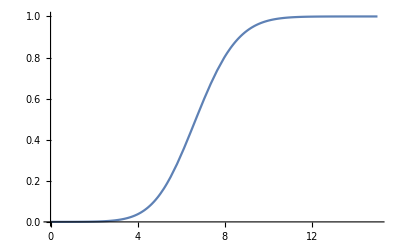

```mathematica
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,0,15}]
```

```mathematica
r1={13,14,15};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
DGIGpdf[r1,r2,m1,m2,1.2,60]
DGIGcdf[r1,r2,m1,m2,1.2,60]
```

0.000620867013379986314913740250052291500166

0.000331315309774187199724803009678492341519

```mathematica
0.0006208670133799863149137402500522915001626186626641978949595018
```

```mathematica
0.0003313153097741871997248030096784923415180213230393108273901091
```

```mathematica
r1={3,4,5};m1={3.4,5.6,7.8};
r2={3,3};m2={12.3,2.3};
(*DGIGquant[r1,r2,m1,m2,.05,-.75]
DGIGquant[r1,r2,m1,m2,.95,1]
DGIGquant2[r1,r2,m1,m2,.05,-.75]
DGIGquant2[r1,r2,m1,m2,.95,1]*)
Timing[DGIGquant[r1,r2,m1,m2,.05,-1,10^-20]]
Timing[DGIGquant[r1,r2,m1,m2,.95,2,10^-20]]
```

{0.078125,-1.0548304132175364316}

{0.15625,2.305457560717974126}

```mathematica
-1.05483041321753643158515171636477044434548793529969
```

```mathematica
2.30545756071797412597809496251918614445065453253009
```

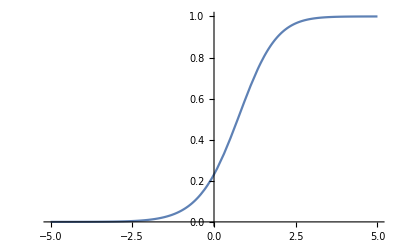

```mathematica
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-5,5}]
```